# Comparing σHe-4 to Schwaller

## Micah Buuck

8/15/13

## Define constants

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ℏc=197.32697178(*Mega ElectronVolt*Femto Meter*);
m=938.272046(*Mega ElectronVolt*);
mn=1.00137842*m(*Mega ElectronVolt*);
r=.535^(-1/2)(*Femto Meter*);
```

## Import data

```mathematica
(*Bdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/B.csv"];
npdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/npsig.csv"];
pndata=Import["/Users/Micah/Documents/JerryDuty/eikexp/pnsig.csv"];
σpndata=Union[npdata,pndata];
αpndata=Import["/Users/Micah/Documents/JerryDuty/eikexp/pnepsilon.csv"];
σppdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/ppsig.csv"];
αppdata=Import["/Users/Micah/Documents/JerryDuty/eikexp/ppepsilon.csv"];*)
```

```mathematica
Bdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/B.csv"];
npdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/npsig.csv"];
pndata=Import["/phys/users/mbuuck/JerryDuty/eikexp/pnsig.csv"];
σpndata=Union[npdata,pndata];
αpndata=Import["/phys/users/mbuuck/JerryDuty/eikexp/pnepsilon.csv"];
σppdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/ppsig.csv"];
αppdata=Import["/phys/users/mbuuck/JerryDuty/eikexp/ppepsilon.csv"];
```

```mathematica
Bdata (*Taken from Schwaller ref 63; slope parameter for scattering amplitude of pp scattering*)
σpndata(*Taken from PDG website; total σ for pn and np collisions*)
αpndata(*From PDG; Re[f(0)]/Im[f(0)] for pn collisions*)
σppdata(*From PDG; total σ for pp collisions*)
αppdata(*From PDG; Re[f(0)]/Im[f(0)] for pp collisions*)
```

{{0.205,1.,6.5},{0.235,0.3,4.4},{0.265,1.9,3.7},{0.355,2.2,1.1},{0.52,0.4,0.6},{0.642,0.4,0.5},{0.778,1.,0.3},{0.81,1.,0.5},{0.864,1.3,0.2},{0.865,1.5,1.3},{0.9,1.9,0.5},{0.91,0.4,0.4},{0.969,1.3,0.3},{0.97,0.9,0.2},{0.971,1.3,0.5},{1.06,1.4,0.2},{1.087,2.1,0.3},{1.13,1.9,0.2},{1.17,2.4,0.2},{1.207,2.3,0.1},{1.21,2.,0.2},{1.215,2.6,0.3},{1.25,2.5,0.1},{1.32,2.1,0.1},{1.372,2.3,0.3},{1.38,2.2,0.1},{1.384,2.8,0.2},{1.45,3.,0.1},{1.453,2.4,0.3},{1.49,1.9,0.1},{1.48,2.5,0.1},{1.71,2.,0.1},{1.87,2.5,0.1},{1.96,2.9,0.2},{1.97,2.7,0.2},{2.11,4.,0.2},{2.13,2.5,0.1},{2.31,3.7,0.2},{2.53,3.5,0.2},{2.72,4.2,0.2}}

{{0.00385,20360.},{0.03043,6202.},{0.03873,4700.},{0.04347,4228.},{0.04502,4060.},{0.04973,3675.},{0.05,3609.5},{0.0502,3630.},{0.051,3542.9},{0.052,3472.1},{0.053,3398.6},{0.05311,3447.},{0.054,3326.5},{0.05448,3330.},{0.055,3266.6},{0.056,3206.6},{0.057,3138.6},{0.058,3079.6},{0.059,3015.5},{0.0597,3004.},{0.06,2963.6},{0.061,2907.2},{0.062,2851.3},{0.063,2792.6},{0.064,2754.},{0.065,2705.5},{0.06571,2677.},{0.066,2651.5},{0.067,2607.4},{0.068,2558.2},{0.069,2507.},{0.06907,2536.},{0.06913,2525.},{0.07,2464.},{0.071,2433.5},{0.07121,2417.},{0.072,2380.4},{0.073,2341.5},{0.074,2295.9},{0.075,2258.5},{0.076,2225.},{0.07633,2274.},{0.077,2185.9},{0.07767,2206.},{0.078,2151.},{0.079,2123.9},{0.08,2091.},{0.081,2049.9},{0.08112,2067.},{0.082,2017.},{0.083,1988.9},{0.084,1945.4},{0.085,1920.},{0.0857,1948.},{0.086,1893.5},{0.087,1864.},{0.08787,1730.},{0.088,1845.},{0.089,1812.5},{0.08999,1829.},{0.09,1782.},{0.091,1744.4},{0.092,1727.},{0.093,1701.8},{0.094,1675.8},{0.0941,1679.},{0.09459,1690.},{0.095,1653.5},{0.096,1626.2},{0.097,1601.1},{0.09798,1620.},{0.098,1577.3},{0.099,1577.2},{0.1,1533.1},{0.101,1516.1},{0.10176,1517.},{0.102,1489.4},{0.103,1468.5},{0.104,1447.1},{0.105,1427.2},{0.10541,1454.},{0.106,1402.},{0.107,1388.6},{0.108,1367.7},{0.109,1346.4},{0.11,1329.8},{0.111,1308.6},{0.112,1290.3},{0.11245,1327.},{0.113,1274.1},{0.114,1255.6},{0.115,1238.1},{0.11564,1263.},{0.116,1218.},{0.1163,1240.},{0.117,1203.},{0.118,1188.},{0.119,1170.8},{0.12,1155.3},{0.121,1138.8},{0.122,1127.5},{0.12287,1134.},{0.123,1109.7},{0.124,1099.6},{0.125,1083.1},{0.126,1066.9},{0.127,1052.4},{0.128,1038.},{0.12867,1040.},{0.129,1024.3},{0.13,1013.8},{0.13047,1026.},{0.131,1002.6},{0.132,990.21},{0.134,965.19},{0.135,948.24},{0.136,938.6},{0.137,927.03},{0.13745,945.},{0.138,913.8},{0.139,902.6},{0.14,892.87},{0.14032,940.},{0.141,883.72},{0.142,874.51},{0.143,863.56},{0.144,853.04},{0.14419,871.},{0.145,844.37},{0.14505,880.},{0.146,832.26},{0.147,820.73},{0.148,811.12},{0.149,800.64},{0.15,793.},{0.15064,809.},{0.151,782.71},{0.152,774.13},{0.153,766.97},{0.15377,690.},{0.154,755.83},{0.155,745.52},{0.156,736.17},{0.15681,749.},{0.157,727.95},{0.15762,760.},{0.158,719.31},{0.159,712.13},{0.15985,694.},{0.16,703.26},{0.161,695.43},{0.162,686.08},{0.1628,686.},{0.1628,690.},{0.16292,720.},{0.163,678.44},{0.16339,689.},{0.16339,690.},{0.164,670.72},{0.165,662.77},{0.166,656.77},{0.167,650.32},{0.168,642.11},{0.16853,640.},{0.16856,662.},{0.169,635.37},{0.17,628.45},{0.171,618.76},{0.17137,648.},{0.172,615.16},{0.173,537.},{0.173,608.56},{0.174,601.03},{0.17413,582.},{0.175,594.86},{0.175,634.},{0.176,588.04},{0.17686,609.},{0.177,580.},{0.177,581.75},{0.178,576.73},{0.178,597.},{0.179,569.24},{0.17954,612.},{0.18,561.},{0.18,563.15},{0.181,558.7},{0.182,544.},{0.182,552.03},{0.18218,587.},{0.183,547.79},{0.18375,560.},{0.184,533.},{0.184,540.36},{0.18479,539.},{0.185,534.22},{0.186,517.},{0.186,526.15},{0.187,522.88},{0.188,518.45},{0.188,523.},{0.189,513.93},{0.19,498.},{0.19,507.95},{0.191,502.9},{0.192,497.93},{0.19274,493.3},{0.19281,498.},{0.193,492.44},{0.193,522.},{0.19324,494.2},{0.19324,495.},{0.194,487.73},{0.19455,504.},{0.195,479.},{0.195,484.43},{0.19519,479.},{0.196,478.55},{0.197,476.},{0.197,479.},{0.19782,470.},{0.198,470.06},{0.19884,467.},{0.199,449.},{0.199,464.2},{0.2,459.5},{0.201,455.9},{0.202,447.},{0.202,450.55},{0.20243,448.},{0.203,446.96},{0.204,420.},{0.204,439.34},{0.20418,432.},{0.205,436.4},{0.206,430.35},{0.207,408.},{0.207,426.59},{0.208,425.55},{0.209,421.4},{0.209,433.},{0.20923,411.},{0.21,418.45},{0.211,397.7},{0.211,414.63},{0.212,408.09},{0.213,403.45},{0.2135,397.2},{0.214,393.},{0.214,401.2},{0.215,395.1},{0.216,393.4},{0.21609,388.},{0.21654,385.5},{0.217,389.59},{0.217,393.5},{0.218,384.68},{0.219,382.49},{0.2195,388.},{0.22,362.9},{0.22,379.59},{0.221,373.55},{0.222,369.6},{0.222,377.6},{0.22263,367.},{0.223,369.64},{0.22395,329.},{0.224,365.89},{0.225,345.7},{0.225,363.53},{0.226,358.2},{0.227,354.29},{0.228,335.4},{0.228,351.4},{0.229,348.},{0.22905,347.},{0.23,345.91},{0.23087,337.6},{0.231,321.5},{0.231,341.61},{0.232,333.5},{0.23234,340.},{0.233,334.3},{0.234,312.2},{0.234,330.7},{0.235,328.9},{0.23524,331.},{0.236,329.4},{0.23626,315.8},{0.237,323.45},{0.238,309.1},{0.238,320.45},{0.239,316.1},{0.24,311.24},{0.241,281.7},{0.241,313.},{0.24118,287.},{0.242,306.52},{0.243,311.6},{0.244,286.4},{0.244,304.1},{0.245,297.2},{0.246,302.5},{0.247,295.94},{0.248,288.7},{0.248,294.5},{0.249,290.19},{0.25,289.3},{0.251,276.},{0.251,287.},{0.252,285.5},{0.255,260.1},{0.259,245.8},{0.263,220.},{0.26383,247.5},{0.267,226.8},{0.26991,223.},{0.272,223.5},{0.27351,227.23},{0.27551,223.7},{0.276,219.1},{0.27707,170.},{0.281,204.6},{0.28406,203.},{0.28406,203.25},{0.286,196.},{0.291,189.1},{0.29426,190.31},{0.296,187.3},{0.29818,185.4},{0.30088,196.},{0.301,170.3},{0.30414,173.38},{0.307,166.8},{0.30757,167.8},{0.312,152.},{0.31375,163.1},{0.318,152.},{0.32309,150.19},{0.32423,151.5},{0.325,144.8},{0.331,141.5},{0.3322,142.64},{0.338,135.8},{0.33919,133.3},{0.3411,134.25},{0.344,124.3},{0.34979,125.21},{0.34979,126.},{0.35122,116.8},{0.3583,118.86},{0.35858,114.9},{0.366,109.6},{0.36664,112.51},{0.37481,107.77},{0.375,100.1},{0.38283,102.88},{0.384,100.3},{0.39071,97.32},{0.393,94.7},{0.39846,93.544},{0.403,85.3},{0.40608,90.375},{0.413,82.1},{0.41359,86.193},{0.41606,84.5},{0.417,85.7},{0.42098,76.},{0.42098,82.783},{0.42098,83.},{0.424,77.7},{0.42826,80.316},{0.42923,77.},{0.43306,73.},{0.43306,73.9},{0.435,72.1},{0.43545,77.676},{0.43782,74.},{0.43829,76.},{0.44,76.6},{0.44253,75.247},{0.447,71.5},{0.44744,80.},{0.44953,73.636},{0.45644,70.841},{0.459,69.4},{0.46054,59.},{0.46326,68.958},{0.468,68.3},{0.47001,67.234},{0.471,68.3},{0.47667,65.355},{0.48327,61.5},{0.48327,63.2},{0.489,62.8},{0.48979,61.82},{0.49625,60.388},{0.5,42.9},{0.50264,56.9},{0.50264,59.424},{0.50897,58.41},{0.51,58.},{0.51524,57.021},{0.52145,56.165},{0.5276,54.876},{0.53168,48.5},{0.533,54.5},{0.5337,53.991},{0.53975,53.367},{0.54575,51.768},{0.5517,51.017},{0.553,51.7},{0.5576,46.4},{0.5576,50.768},{0.56346,50.425},{0.56346,50.5},{0.56927,49.544},{0.57119,51.2},{0.57503,48.831},{0.58076,47.936},{0.58645,47.638},{0.58833,49.2},{0.59,40.9},{0.59209,46.318},{0.5977,45.961},{0.60327,45.272},{0.60881,44.},{0.60881,45.05},{0.61431,44.501},{0.61977,43.976},{0.6252,43.446},{0.6306,43.254},{0.63597,42.87},{0.64131,42.022},{0.64485,41.918},{0.64501,42.7},{0.66,37},{0.66236,41.04},{0.66582,42.46},{0.67957,39.966},{0.67957,41.},{0.67957,41.3},{0.69649,38.963},{0.71316,38.085},{0.725,42.8},{0.72958,37.144},{0.74577,36.819},{0.75857,38.13},{0.76175,33.},{0.76175,36.355},{0.76175,38.},{0.775,38.63},{0.77753,35.582},{0.79313,35.106},{0.80854,34.563},{0.82379,34.56},{0.825,37.32},{0.83,32.5},{0.83738,36.14},{0.83888,34.1},{0.85382,33.938},{0.86862,33.487},{0.875,33.97},{0.88329,33.749},{0.89783,33.163},{0.9108,35.05},{0.91224,32.68},{0.925,34.09},{0.92654,32.685},{0.94,32},{0.94073,32.771},{0.95481,32.417},{0.96879,32.408},{0.96879,33.7},{0.975,33.9},{0.97851,34.53},{0.98267,32.548},{0.99646,32.914},{1.01016,32.41},{1.02377,32.634},{1.024,33.57},{1.03731,32.714},{1.05076,32.952},{1.06414,32.813},{1.075,34.16},{1.07744,33.154},{1.08,31.8},{1.08407,35.15},{1.09067,33.308},{1.10384,33.139},{1.11,35.72},{1.11694,33.231},{1.125,34.94},{1.12998,33.055},{1.14295,33.623},{1.15587,34.021},{1.16873,33.732},{1.175,35.47},{1.18153,34.662},{1.19,30.7},{1.19428,34.354},{1.20698,34.609},{1.21962,35.318},{1.225,36.04},{1.23222,34.665},{1.24,31.1},{1.24478,35.347},{1.25728,35.2},{1.25728,35.875},{1.26974,35.745},{1.275,36.85},{1.28,31.7},{1.28216,36.117},{1.29,38.64},{1.29454,36.486},{1.30688,36.953},{1.31917,37.415},{1.325,37.6},{1.33143,37.19},{1.34365,37.357},{1.35584,37.848},{1.36798,38.197},{1.375,37.85},{1.3801,38.493},{1.39218,38.263},{1.40423,38.241},{1.41,39.44},{1.41624,38.656},{1.425,37.98},{1.42823,38.318},{1.5,37.82},{1.59,39.2},{1.6,38.12},{1.61,39.77},{1.66,40.09},{1.7,38.21},{1.78,40.56},{1.8,38.85},{1.86,41.22},{1.9,39.35},{1.94,41.53},{1.95,41.48},{2.022,39.99},{2.08,41.91},{2.14261,42.4},{2.193,40.5},{2.21,42.17},{2.28,42.5},{2.391,40.67},{2.45,42.68},{2.59,42.89},{2.627,40.75},{2.68,42.96},{2.7,42.93},{2.82,43.02},{2.86,43.04},{2.944,40.76},{2.96,43.11},{2.99,43.12},{3.,43.},{3.05,42.98},{3.11,43.23},{3.14,43.12},{3.27,37.1},{3.277,40.83},{3.28,42.81},{3.3,42.99},{3.4126,38.1},{3.44,42.58},{3.55,42.52},{3.91,42.53},{4.,43.1},{4.04,42.5},{4.26,42.28},{4.3,40.4},{4.51,36.8},{4.55,42.26},{4.7476,43.4},{4.97,42.07},{5.22,42.02},{5.53,42.03},{5.7,42.5},{5.82,41.82},{5.83,37},{5.86478,33.6},{6,42.6},{6.3706,41.2},{6.37066,41.2},{6.5,38.7},{7.75,37.6},{7.7831,39.3},{7.84,41.33},{8,41.8},{8.,39.7},{8.2468,41.2},{9.1919,40.8},{10,41.5},{10.,39.5},{11.,39.4},{12,40.4},{12.,39.3},{13.,39.},{14,40.2},{14.,38.7},{14.6,37.1},{15,39.68},{16,40.2},{16.,39.1},{17.,38.5},{17.8,37.5},{18,39.2},{18.,38.7},{19.8,38.7},{20,38.7},{20,39.06},{21.,38.5},{21.6,37.7},{22,38.2},{23,38.52},{25,38.79},{26.2832,38.94},{26.5,39.3},{27.,38.9},{30,38.84},{34.,38.2},{35,38.58},{35,39.15},{36.5879,38.85},{40,38.65},{45,38.28},{50,38.5},{50,38.86},{50,38.96},{52.6916,38.2},{55,38.35},{60,38.51},{70,38.95},{80.,38.98},{100,38.85},{100,38.96},{120,39.02},{131.,39.14},{131.,39.17},{133.,39.21},{150,39.02},{150,39.07},{170,39.18},{175.,39.21},{180.,39.52},{180.,39.62},{200,39.18},{200,39.27},{215.,39.79},{240,39.5},{240.,39.66},{273.,40.32},{280,39.53},{310,39.75},{310.,39.6},{340,39.72},{370,40.01}}

{{0.6,-0.48},{1.69,-0.5},{11.2,-0.21},{15.9,-0.38},{20.5,-0.35},{26.5,-0.35},{34.8,-0.25},{48.9,-0.14},{48.991,-0.081},{57.2,-0.2},{64.8,0.13},{70.2,-0.14},{81.9946,-0.127},{181.998,-0.065},{280.998,-0.084},{378.999,-0.045},{396.999,0.021}}

{{0.14,314},{0.19,155},{0.24,92},{0.28,70},{0.31,52.8},{0.35,42.5},{0.37,37.4},{0.39,33.9},{0.43,28.5},{0.44,27.7},{0.49,24.8},{0.54,25.2},{0.57,26.1},{0.59,23.2},{0.60658,24.2},{0.607,24.55},{0.65847,25.8},{0.69,22.4},{0.72,22.4},{0.75,22.6},{0.757,23.85},{0.75732,23.85},{0.83,24.3},{0.83086,24.3},{0.846,24.4},{0.85,23.4},{0.87179,24.55},{0.872,24.45},{0.88,23.2},{0.93,24.4},{0.937,25.65},{0.93736,25.7},{0.963,26.3},{0.96336,26.5},{0.96545,24},{0.96824,26.9},{0.96824,26.5},{1,28},{1.00549,23.8},{1.00891,27.95},{1.009,27.75},{1.00959,27},{1.03673,28},{1.03673,27.6},{1.09008,29.9},{1.093,30.95},{1.09337,31.25},{1.10783,31.95},{1.108,31.65},{1.111,34.029},{1.111,32.9},{1.127,30},{1.13586,29.8},{1.14234,32.1},{1.16168,34.8},{1.162,34.5},{1.19365,35.6},{1.20634,36},{1.215,39},{1.21898,36.6},{1.23786,37.7},{1.24413,38.6},{1.26909,39.8},{1.2814,41.8},{1.289,43.234},{1.29017,41},{1.29388,41.4},{1.323,43},{1.39149,44.4},{1.408,46.487},{1.42,46.2},{1.424,46},{1.46329,47},{1.49881,47.8},{1.52235,47.6},{1.531,47.4},{1.5458,47.94},{1.5924,46.1},{1.6,47.5},{1.607,47.476},{1.628,49},{1.66,47.553},{1.687,48},{1.69604,48},{1.69604,47.4},{1.73,46.2},{1.78,47.49},{1.78127,48.3},{1.785,47},{1.858,47.455},{1.886,47.4},{1.89,46.8},{1.94,47.357},{1.952,47.409},{1.99,47},{2.00455,47.5},{2.02661,49.4},{2.05,45.3},{2.079,47.224},{2.212,46.985},{2.23968,47.2},{2.28,46.669},{2.419,46.13},{2.45,45.827},{2.47,45.1},{2.592,45.533},{2.68,45.331},{2.704,45.174},{2.78444,41.4},{2.819,45.008},{2.857,44.928},{2.88976,45.54},{2.958,44.651},{2.97,44.5},{2.994,44.466},{3.054,44.401},{3.11,44.188},{3.131,44.156},{3.142,44.114},{3.27,47.1},{3.277,43.61},{3.303,43.669},{3.4116,41.6},{3.444,43.138},{3.546,42.978},{3.58,43.2},{3.67024,42.1},{3.731,42.68},{3.908,42.316},{4,43},{4,41.6},{4.037,42.136},{4.15,39.7},{4.2,42.2},{4.265,41.765},{4.5099,42.1},{4.552,41.457},{4.783,41.377},{4.966,41.165},{5.221,41.171},{5.52,41.6},{5.526,40.878},{5.824,40.848},{5.8302,41.6},{5.96493,38.3},{6,40.6},{7,40.6},{7.7502,41.6},{7.835,40.075},{7.85,40},{8,40},{8.1,40.1},{9.9002,39.4},{10,39.9},{10,39.6},{10,40.2},{10.01,41.1},{10.11,40},{12,39.4},{12,39.6},{12.4,39},{14,39.1},{15,39.29},{15.8,38.7},{16,38.7},{17.7,39.7},{18,38.7},{19.33,38.9},{19.4,39.7},{19.8,38.6},{20,38.4},{20,39.06},{20,38.85},{21.4,39.4},{22,38.3},{23,39.39},{23.5,39.7},{24,38.9},{24.2,38.7},{24.5,39.3},{25,38.8},{26.42,38.8},{28.4,39.9},{30,38.59},{30,38.55},{32.1,38.4},{35,38.49},{35,38.46},{40,38.5},{40,38.85},{42.5,38.42},{45,38.45},{50,38.46},{50,38.2},{50,38.14},{50,38.42},{50,37.74},{52.2,37.87},{55,38.43},{60,38.44},{65,38.65},{69,36.68},{70,38.28},{72.994,37.6},{97.9955,37.6},{100,38.7},{100,38.46},{100,38.39},{102,38.9},{120,38.58},{121.996,37},{146.997,37.6},{147,38.47},{150,38.69},{150,38.62},{170,38.83},{171.997,37.4},{175,39.6},{195.998,38.5},{200,38.98},{200,38.9},{205,39},{240,39.24},{280,39.42},{293.352,39.65},{293.352,39.4},{293.352,39.13},{293.352,38.8},{293.352,38.9},{295.862,38.7},{300,39.21},{300,40.68},{303,39},{310,39.59},{340,39.69},{370,39.77},{405,40.6},{498.043,40.22},{498.043,40.11},{498.043,39.91},{498.043,40.07},{498.043,40.2},{498.05,40.1},{501.31,40.1},{504.587,40},{659.34,40.42},{1063.8,41.7},{1063.83,41.9},{1073.38,41.89},{1087.79,42.5},{1484.69,43.01},{1484.69,42.38},{1484.69,42.1},{1484.69,42.85},{1484.69,42.71},{1490.3,42.4},{1507.28,42.9},{2067.38,43.55},{2074.1,43.1},{2080.69,44},{2094.03,43.82},{2094.03,42.96},{2100.72,44.1},{2114.12,42.2},{3982,43},{10000.,48},{20000.,54},{39800.,56},{79400.,54},{2.02×10^7,93},{2.61×10^7,98.3},{3.52×10^7,101},{6.11×10^7,117},{1.06×10^8,104},{1.85×10^8,100},{3.21×10^8,124},{4.8×10^8,120}}

{{0.13526,0.8},{0.16033,0.85},{0.22067,1.1},{0.27475,1.7},{0.31511,2},{0.36446,1.73},{0.55134,1.46},{0.66714,1},{0.82633,0.65},{0.85332,-0.09},{0.87546,-0.3},{0.926,0.59},{1.00276,0.41},{1.03673,-0.77},{1.09008,0.78},{1.10717,0.25},{1.1681,-0.74},{1.25663,0.53},{1.27902,0.249},{1.27902,0.284},{1.29,-0.76},{1.29017,-0.256},{1.30621,0.4},{1.34053,0.248},{1.39,-0.58},{1.40353,0.01},{1.54,-0.3},{1.54,-0.32},{1.66167,0.06},{1.68689,-0.186},{1.69,0.1},{1.69032,-0.17},{1.7,-0.007},{2.78444,-0.12},{3,-0.426},{4.2,-0.39},{4.84831,-0.38},{5,-0.389},{6.87454,-0.3},{7,-0.339},{7,-0.4},{7.81,-0.331},{7.85,-0.29},{8.88889,-0.33},{9.43,-0.351},{9.86,-0.343},{9.86,-0.345},{10,-0.33},{10,-0.31}}

```mathematica
(*σHe4data={{{224,106.3},ErrorBar[1.3]},{{273,105.7},ErrorBar[1.3]},{{345,106.8},ErrorBar[1.1]},{{413,110.8},ErrorBar[1.2]},{{430,112.8},ErrorBar[1.0]},{{491,117.6},ErrorBar[1.5]},{{563,123.7},ErrorBar[0.9]}};*)
```

```mathematica
σHe4data={{224,106.3},{273,105.7},{345,106.8},{413,110.8},{430,112.8},{491,117.6},{563,123.7}};
```

## Do a linear fit of the B data:

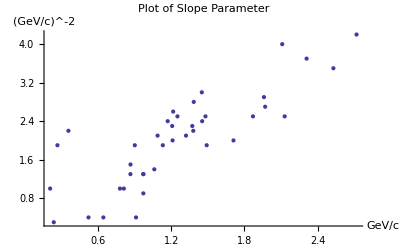

```mathematica
ListPlot[Bdata[[All,1;;2]],PlotLabel->"Plot of Slope Parameter",AxesLabel->{"GeV/c","(GeV/c)^-2"}]
```

```mathematica
Bmodel=LinearModelFit[Bdata[[All,1;;2]],x,x]
```

FittedModel[0.401428+1.29697 x]

```mathematica
Clear[B]
```

```mathematica
Bfunc[x_]=Bmodel["BestFit"];
```

Get slope parameter in units and form matching Schwaller paper:

```mathematica
gamma[En_(*MeV*)]=Sqrt[Bfunc[Sqrt[(En/1000)^2+2*m/1000*En/1000]]]*(ℏc/1000)*Sqrt[2](*fm*);
```

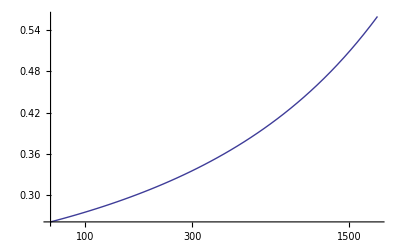

```mathematica
LogLinearPlot[gamma[En],{En,70,2000}]
```

## Fit Bezier Curve to σ and α data

```mathematica
σpnbf=BezierFunction[DeleteDuplicates[Log[σpndata],#1[[1]]==#2[[1]]&]];
```

```mathematica
Show[Graphics[{Red,Point[Log[σpndata]]},Axes->True],ParametricPlot[σpnbf[t],{t,0,1}],PlotLabel->"Log-Log Plot of total σ for pn scattering with fitted curve",AxesLabel->{Log[p]"in GeV/c  ",Log[σ]"in mb  "}]
```

-Graphics-

```mathematica
σpnbf[[3]]
```

{592}

```mathematica
σpng=Interpolation[σpnbf/@Range[0,1,.001]];
```

It takes some processing to get the fit into a useable function

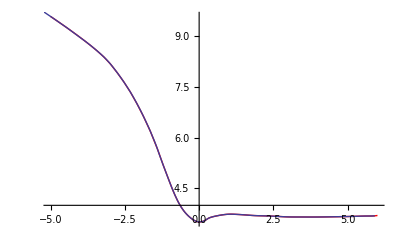

```mathematica
σpnp1=Plot[σpng[x],{x,-5,6},PlotStyle->Red];
σpnp2=ParametricPlot[σpnbf[t],{t,0,1}];
Show[σpnp1,σpnp2]
```

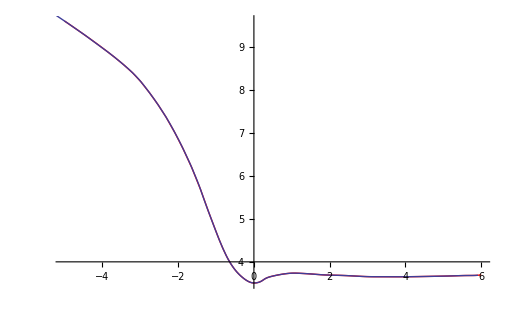

-Graphics-

```mathematica
σpn[En_(*MeV*)]=Exp[σpng[Log[Sqrt[(En/1000)^2+2*m/1000*En/1000]]]]/10;
```

The line above unlogs the Bezier fit and converts it into the right units (fm^2).

```mathematica
σpn[2000](*in fm^2*)
```

4.19813

The plot below shows that it fits the raw unloged data well.

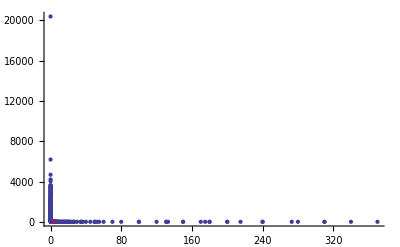

```mathematica
Show[ListPlot[σpndata],Plot[Exp[σpng[Log[x]]],{x,.00385,7},PlotStyle->Red]]
```

Now we repeat the same process for α, and then for both σand α for pp scattering.

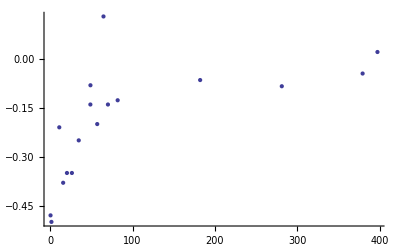

```mathematica
ListPlot[αpndata]
```

```mathematica
αpnbf=BezierFunction[DeleteDuplicates[αpndata,#1[[1]]==#2[[1]]&]];
```

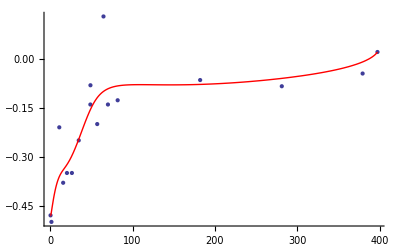

```mathematica
Show[ListPlot[αpndata],ParametricPlot[αpnbf[t],{t,0,1},PlotStyle->Red]]
```

```mathematica
αpng=Interpolation[αpnbf/@Range[0,1,.001]];
```

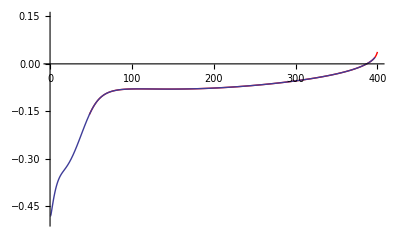

```mathematica
αpnp1=Quiet[Plot[αpng[x],{x,0,400},PlotStyle->Red]];
αpnp2=ParametricPlot[αpnbf[t],{t,0,1}];
Show[αpnp1,αpnp2,PlotRange->{-.5,.15}]
```

```mathematica
αpn[En_(*MeV*)]:=αpng[Sqrt[(En/1000)^2+2*m/1000*En/1000]]
```

```mathematica
σppbf=BezierFunction[DeleteDuplicates[Log[σppdata],#1[[1]]==#2[[1]]&]];
```

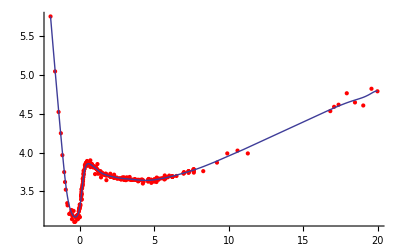

```mathematica
Show[ListPlot[Log[σppdata],PlotStyle->Red],ParametricPlot[σppbf[t],{t,0,1}]]
```

```mathematica
σppg=Interpolation[σppbf/@Range[0,1,.001]]
```

InterpolatingFunction[{{-1.96611,19.9893}},<>]

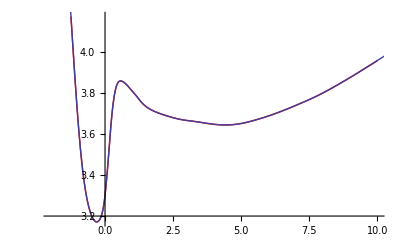

```mathematica
σppp1=Quiet[Plot[σppg[x],{x,-2,10},PlotStyle->Red]];
σppp2=ParametricPlot[σppbf[t],{t,0,1}];
Show[σppp1,σppp2]
```

```mathematica
σpp[En_(*MeV*)]=Exp[σppg[Log[Sqrt[(En/1000)^2+2*m/1000*En/1000]]]]/10;
```

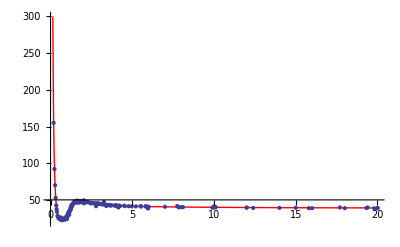

```mathematica
Show[Plot[Exp[σppg[Log[x]]],{x,.14,20},PlotStyle->Red,PlotRange->{{0,20},{20,300}}],ListPlot[σppdata]]
```

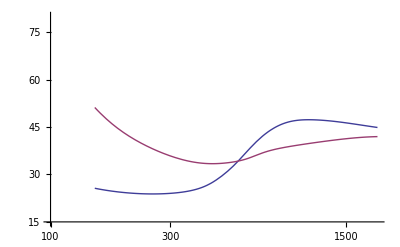

```mathematica
Quiet[LogLinearPlot[{10*σpp[En],10*σpn[En]},{En,150,2000},PlotRange->{{100,2000},{15,80}}]]
```

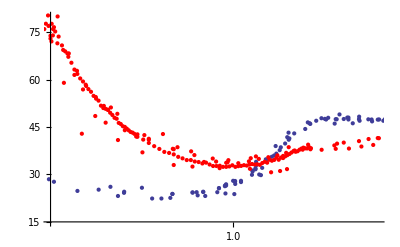

```mathematica
Show[ListLogLinearPlot[σppdata,PlotRange->{{Sqrt[2*m/1000*100/1000],Sqrt[2*m/1000*2000/1000]},{15,80}}],ListLogLinearPlot[σpndata,PlotStyle->Red]]
```

Take average of σpn and σpp to get nucleon-nucleon scattering. (This is what Schwaller does.)

```mathematica
σ[En_(*MeV*)]=(σpp[En]+σpn[En])/2;
```

```mathematica
σ[2000]
```

4.34266

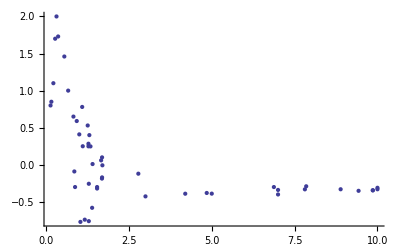

```mathematica
ListPlot[αppdata]
```

```mathematica
αppbf=BezierFunction[DeleteDuplicates[αppdata,#1[[1]]==#2[[1]]&]];
```

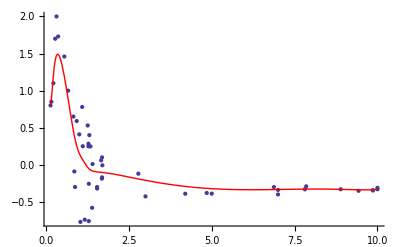

```mathematica
Show[ListPlot[αppdata],ParametricPlot[αppbf[t],{t,0,1},PlotStyle->Red]]
```

```mathematica
αppg=Interpolation[αppbf/@Range[0,1,.001]];
```

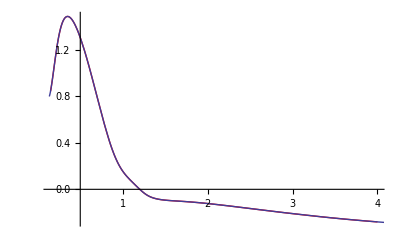

```mathematica
αppp1=Plot[αppg[x],{x,.15,4},PlotStyle->Red];
αppp2=ParametricPlot[αppbf[t],{t,0,1}];
Show[αppp1,αppp2]
```

```mathematica
αpp[En_(*MeV*)]:=αppg[Sqrt[(En/1000)^2+2*m/1000*En/1000]]
```

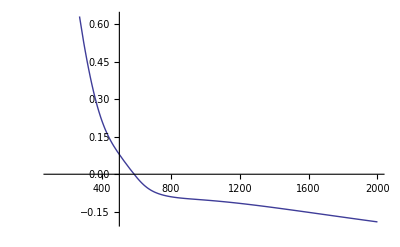

```mathematica
Plot[αpp[En],{En,100,2000}]
```

Take average of αpn and αpp to get α for nucleon-nucleon scattering.

```mathematica
(*α[En_(*MeV*)]=If[En<500,Log[500/En],Log[500/En]/2];*)
α[En_(*MeV*)]=(αpn[En]+αpp[En])/2;
```

This average might not be so good, because the energy range in question only contains about two data points for αpn. There are many more data points for αpp in the energy region of interest, so it may just be better to take αpp as the overall α instead of an average (or perhaps use some sort of weighting process).

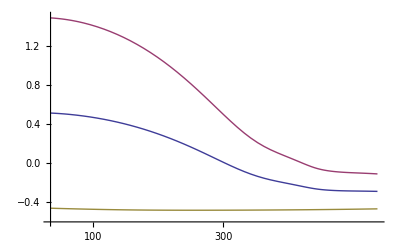

```mathematica
Quiet[LogLinearPlot[{α[En],αpp[En],αpn[En]},{En,70,1100},PlotRange->{-.6,1.5}]]
```

```mathematica
σHe4[En_(*MeV*)]:=20*Pi*r^2*(1+2*r^(-2)*gamma[En]^2)*Sum[Binomial[4,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*r^2*(1+2*r^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,4}](*This is in mb*)
```

```mathematica
σHe4[500]
```

108.627

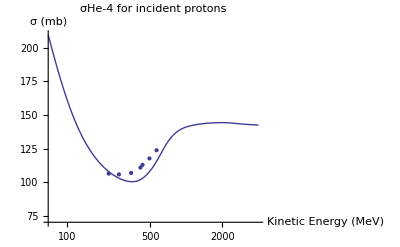

```mathematica
σHe4LLP=Quiet[LogLinearPlot[σHe4[En],{En,70,4000},PlotRange->{{70,4000},{70,210}},PlotLabel->"σHe-4 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]];
σHe4LP=ListLogLinearPlot[σHe4data];
Show[σHe4LLP,σHe4LP]
```

This plot seems to roughly follow what Schwaller has in his paper. There seems to be some disagreement at low energies. At ~150 MeV, Schwaller’s σ ≃ 160 mb, but I have σ ≃ 120 mb. This actually seems to fit the data better than Schwaller’s analysis, which is strange, since I followed it as best I could. My best guess as to what may be causing this discrepancy is that I believe he was using values for his slope parameter that were quite different from mine. He comments that above about 500 MeV, a value of gamma^2 = 0.3 fm^2 seems to fit the data well. That does not agree with what I found:

```mathematica
gamma[500]^2
```

0.141362

It is also possible that the more recent and probably accurate data I am using from the PDG is better than what he had, and that that helps with accuracy.

Here I can test the effect using αpp instead of α has on the calculation:

```mathematica
σHe41[En_(*MeV*)]:=20*Pi*r^2*(1+2*r^(-2)*gamma[En]^2)*Sum[Binomial[4,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*r^2*(1+2*r^-2*gamma[En]^2)))^j*Re[(1-I*αpp[En])^j],{j,1,4}](*This is in mb*)
```

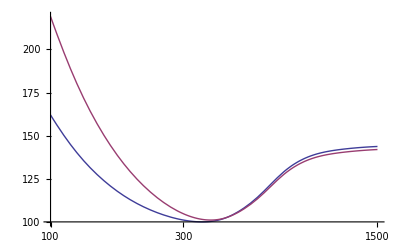

```mathematica
Quiet[LogLinearPlot[{σHe4[En],σHe41[En]},{En,100,1500}]]
```

It appears to have quite a large effect. This is alarming, since the data for αpn was so sparse.

With just some very basic eyeballing, it looks like the fits that Schwaller made for α are approximately the curve below. Check out Fig 7 (solid line) and compare:

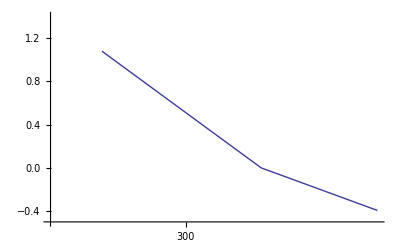

```mathematica
LogLinearPlot[If[x<500,Log[500/x],Log[500/x]/2],{x,170,1100},PlotRange->{{120,1100},{-.5,1.4}}]
```

```mathematica
rC12=.263^(-1/2);
```

```mathematica
σC12[En_]:=20*Pi*rC12^2*(1+2*rC12^(-2)*gamma[En]^2)*Sum[Binomial[12,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*rC12^2*(1+2*rC12^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,12}](*This is in mb*)
```

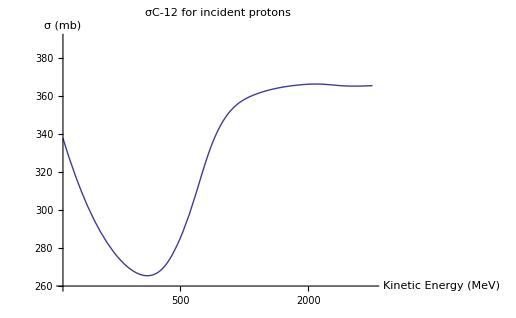

```mathematica
Quiet[LogLinearPlot[σC12[En],{En,140,4000},PlotRange->{{140,4000},{260,390}},PlotLabel->"σC-12 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]]
```

```mathematica
rO16=.233^(-1/2);
```

```mathematica
σO16[En_]:=20*Pi*rO16^2*(1+2*rO16^(-2)*gamma[En]^2)*Sum[Binomial[16,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*rO16^2*(1+2*rO16^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,16}](*This is in mb*)
```

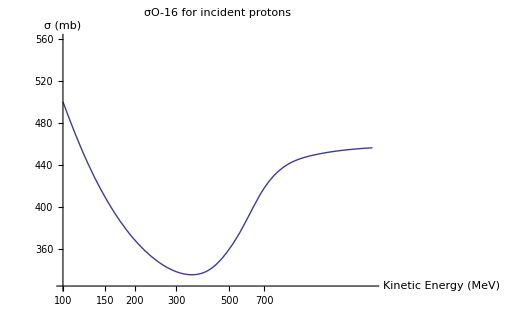

```mathematica
Quiet[LogLinearPlot[σO16[En],{En,100,2000},PlotRange->{{100,2000},{325,560}},PlotLabel->"σO-16 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]]
```

```mathematica
rH2=.2^(-1/2);
```

```mathematica
σH2[En_]:=20*Pi*rH2^2*(1+2*rH2^(-2)*gamma[En]^2)*Sum[Binomial[2,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*rH2^2*(1+2*rH2^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,2}]
```

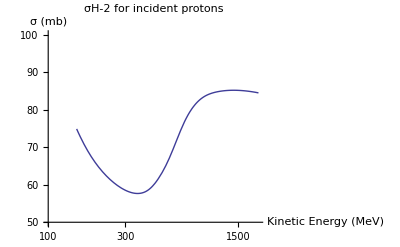

```mathematica
Quiet[LogLinearPlot[σH2[En],{En,150,2000},PlotRange->{{100,2000},{50,100}},PlotLabel->"σH-2 for incident protons",AxesLabel->{"Kinetic Energy (MeV)","σ (mb)"}]]
```

## Add in first order correction

Going to switch over to Wallace's notation now:

```mathematica
m=0.938272046;(*GeV/c^2*)
mn=1.00137842*m(*GeV/c^2*);
M=2*m+2*mn;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
gamma[En_(*GeV*)]:=Sqrt[Bfunc[Sqrt[En^2+2*m*En]]]*ℏc*Sqrt[2](*fm*)
β[En_(*GeV*)]:=1/2*gamma[En]^2/ℏc^2(*(c/GeV)^2*)
B:=1/4*r^2/ℏc^2(*(c/GeV)^2*)
αpn[En_(*GeV*)]:=αpng[Sqrt[En^2+2*m*En]]
αpp[En_(*GeV*)]:=αppg[Sqrt[En^2+2*m*En]]
α[En_(*GeV*)]:=(αpp[En]+αpn[En])/2
ρ[En_(*GeV*)]:=α[En]
σpn[En_(*GeV*)]:=Exp[σpng[Log[Sqrt[En^2+2*m*En]]]]/10
σpp[En_(*GeV*)]:=Exp[σppg[Log[Sqrt[En^2+2*m*En]]]]/10
σ[En_(*GeV*)]:=(σpp[En]+σpn[En])/2
σ1[En_(*GeV*)]:=σ[En]*(1-I*ρ[En])/(8*Pi*β[En]*ℏc^2)
A=4;
myLog[z_]:=Log[Abs[z]]+I*If[Im[z]<0,Arg[z ]+2*Pi,Arg[z]]
```

There is a big problem with the calculation of the eikonal potential given by equation 30. It has to do with the fact that at a certain energy, the argument of the Logarithm inside of the integral goes over its branch cut and has a discontinuity. I tried moving the branch cut, but that did not help.

```mathematica
temp=Piecewise[{{NIntegrate[b*BesselJ[0,b*q]*(Log[Abs[1-σ1[En]*Exp[-b^2/(4*β[En])]]]-I*Arg[1-σ1[En]*Exp[-b^2/(4*β[En])]]),{b,0,100}],En<0.30508486005825836},{NIntegrate[b*BesselJ[0,b*q]*Log[1-σ1[En]*Exp[-b^2/(4*β[En])]],{b,0,100}],En>0.30508486005825836}}];
```

```mathematica
Utest[x_,y_(*GeV*)]:=2*Pi*I*temp/.{q->x,En->y}
```

```mathematica
U[q_,En_(*GeV*)]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-σ1[En]*Exp[-b^2/(4*β[En])]],{b,0,100}]
```

```mathematica
Ualt[q_,En_]:=-I*Pi/(β[En]*q)*NIntegrate[b^2*BesselJ[1,q*b]*σ1[En]*Exp[-b^2/(4*β[En])]/(1-σ1[En]*Exp[-b^2/(4*β[En])]),{b,0,100}]
```

```mathematica
g=Piecewise[{{Log[Abs[Ualt[1,En]]]+I*(Arg[Ualt[1,En]]-2*Pi)-Log[Ualt[0.0000001,En]],En<0.263091},{Log[Ualt[1,En]]-Log[Ualt[0.0000001,En]],En>0.263091}}];
```

```mathematica
γ[x_]:=g/.En->x
```

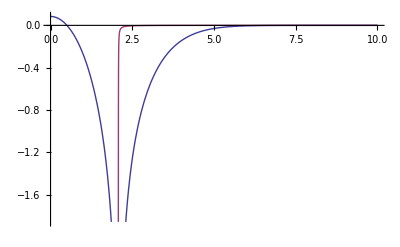

```mathematica
Plot[{Re[Log[1-σ1[.306]*Exp[-b^2/(4*β[.306])]]],Im[Log[1-σ1[.306]*Exp[-b^2/(4*β[.306])]]]},{b,0,10}]
```

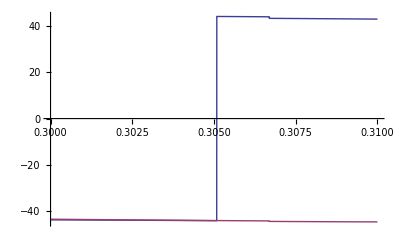

```mathematica
Plot[{Re[U[0,En]],Im[U[0,En]]},{En,.3,.31}]
```

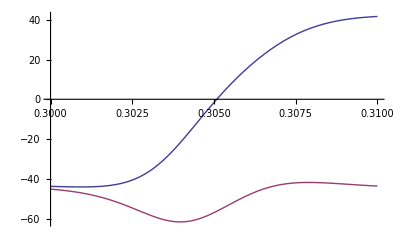

```mathematica
Plot[{Re[Ualt[0.00001,En]],Im[Ualt[0.00001,En]]},{En,.3,.31}]
```

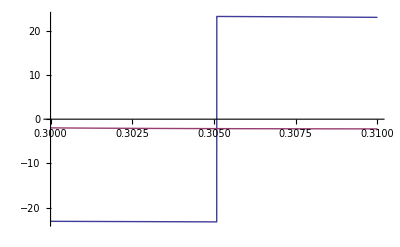

```mathematica
Plot[{Re[U[1,En]],Im[U[1,En]]},{En,.3,.31}]
```

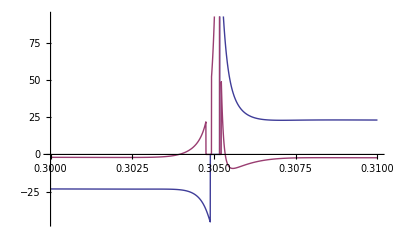

```mathematica
Plot[{Re[Ualt[1,En]],Im[Ualt[1,En]]},{En,.3,.31}]
```

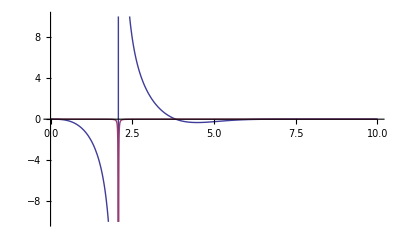

```mathematica
Plot[{Re[b^2*BesselJ[1,1*b]*σ1[.305]*Exp[-b^2/(4*β[.305])]/(1-σ1[.305]*Exp[-b^2/(4*β[.305])])],Im[b^2*BesselJ[1,1*b]*σ1[.305]*Exp[-b^2/(4*β[.305])]/(1-σ1[.305]*Exp[-b^2/(4*β[.305])])]},{b,0,10},PlotRange->{-10,10}]
```

```mathematica
Plot[{Re[σ1[En]],Im[σ1[En]]},{En,.07,4}]
```

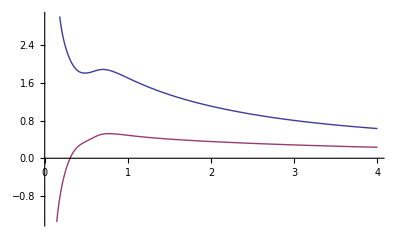

```mathematica
FindRoot[Im[σ1[x]]==0,{x,.3}]
```

{x→0.305085}

Other discontinuity is at En = 0.263091 GeV. This occurs because the

σ1 has a zero in its imaginary part at about 0.305085 GeV, which appears to create quite a few problems in the parameters that are used in the corrections.

I decided to interpolate a smooth curve to the following two parameters, so that Mathematica wouldn't have to integrate every time they were called. This speeded up things tremendously.

```mathematica
Z=Quiet[Interpolation[Table[{En,U[0,En]/(-I*4*Pi*σ1[En]*β[En])},{En,.31,4.1,.1}]]];(*Unitless*)
g1=Quiet[Interpolation[Table[{En,(Log[U[0,En]]-Log[U[1,En]])},{En,.1,.263090,.1}]]];
g2=Quiet[Interpolation[Table[{En,(Log[U[0,En]]-Log[U[1,En]])},{En,.263091,.305084,.1}]]];
g3=Quiet[Interpolation[Table[{En,(Log[U[0,En]]-Log[U[1,En]])},{En,.305085,4.1,.1}]]];
g=Quiet[Piecewise[{{g1[En],En<.263090},{g2[En],.263090<En<.305085},{g3[En],.305085<En}}]];(*(c/GeV)^2*)
γ[x_]:=g/.En->x
```

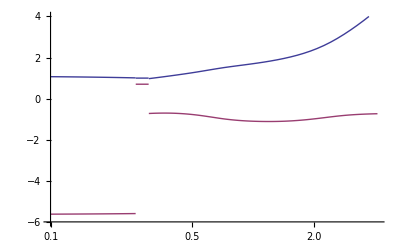

```mathematica
LogLinearPlot[{Re[γ[En]],Im[γ[En]]},{En,.1,4.1},PlotRange->{-6,4}]
```

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1[En_]:=γ[En]*β[En]/(γ[En]+β[En])(*(c/GeV)^2*)
αnL[En_,n_,L_]:=If[n==1,(2*(γ[En]+B)^-1+L*(β[En]+B)^-1)^-1,If[n==2,((γ[En]+B)^-1+(γ1[En]+B)^-1+L*(β[En]+B)^-1)^-1,If[n==3,(2*(γ1[En]+B)^-1+L*(β[En]+B)^-1)^-1]]]
an[En_,n_]:=If[n==1,(γ[En]+B)^-2,If[n==2,-2*σ1[En]*(γ1[En]/γ[En])*(γ[En]+B)^-1*(γ1[En]+B)^-1,If[n==3,σ1[En]^2*(γ1[En]/γ[En])^2*(γ1[En]+B)^-2]]]
bn[En_,n_]:=If[n==1,(γ[En]+B)^-3,If[n==2,-σ1[En]*(γ1[En]/γ[En])*(γ1[En]+B)^-1*(γ[En]+B)^-1*((1-B*γ1[En]/(β[En]*(B+γ1[En])))/(γ[En]+B)+(1-γ1[En]/β[En])/(γ1[En]+B)),If[n==3,σ1[En]^2*(γ1[En]/γ[En])^2*(γ1[En]+B)^-3*(1-B*γ1[En]/(β[En]*(B+γ1[En])))*(1-γ1[En]/β[En])]]]
γ2[En_]:=γ[En]*β[En]/(β[En]+2*γ[En])(*(c/GeV)^2*)
βnL[En_,n_,L_]:=If[n==1,((γ[En]/2+B)^-1+L*(β[En]+B)^-1)^-1,If[n==2,((γ2[En]/2+B)^-1+L*(β[En]+B)^-1)^-1]]
cn[En_,n_]:=If[n==1,(γ[En]-2*B)*(γ[En]+2*B)^-2,If[n==2,-σ1[En](γ2[En]/γ1[En])*(γ2[En]+2*B)^-1*(1-2*γ2[En]/γ[En]+2*(γ2[En])^2/(γ[En]*(γ2[En]+2*B)))]]
dn[En_,n_]:=If[n==1,γ[En]*(γ[En]+2*B)^-3,If[n==2,
-σ1[En]*(γ[En])^-2*(γ2[En]/(γ2[En]+2*B))^3]]
```

```mathematica
Fcm[q_]:=Exp[B*q^2/A]
EnL[En_]:=En+m
s[En_]:=m^2+M^2+2*M*EnL[En]
ϵ[En_]:=EnL[En]/(M/Sqrt[s[En]])
P[En_]:=Sqrt[EnL[En]^2-m^2]
k[En_]:=P[En]*(M/Sqrt[s[En]])
s2[En_]:=m^2+m^2+2*m*EnL[En]
ϵ2[En_]:=EnL[En]*(m/Sqrt[s2[En]])
κ[En_]:=P[En]*(m/Sqrt[s2[En]])
ηO[En_]:=(1-ϵ[En]/M)*(m+M)/Sqrt[s[En]]
ηD[En_]:=(1-ϵ[En]/ϵ2[En]+(A-1)*ϵ[En]/M)*(m+M)/Sqrt[s[En]]
```

```mathematica
F0[En_(*GeV/c^2*),q_]:=-2*I*k[En]*Fcm[q]*(B+β[En])*Sum[Binomial[A,j]/j*(-σ[En]*(1-I*ρ[En])/(8*Pi*(B+β[En])*ℏc^2))^j*Exp[-(B+β[En])*q^2/j],{j,1,A}]*ℏc
```

```mathematica
σHe4[En_(*MeV*)]:=20*Pi*r^2*(1+2*r^(-2)*gamma[En]^2)*Sum[Binomial[4,j]*(-1)^(j+1)/j*(σ[En]/(2*Pi*r^2*(1+2*r^-2*gamma[En]^2)))^j*Re[(1-I*α[En])^j],{j,1,4}](*This is in mb*)
```

```mathematica
FO1 [En_(*GeV/c^2*),q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO[En]*(β[En]*σ1[En]*Z[En])^2/(2*(2*Pi*(B+β[En]))^(1/2))*Sum[Binomial[A-2,L]*(-σ1[En]*β[En]/(B+β[En]))^L*Sum[αnL[En,n,L]*(an[En,n]-4*αnL[En,n,L]*bn[En,n]*(1-αnL[En,n,L]q^2))*Exp[-αnL[En,n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[En_(*GeV/c^2*),q_(*c/GeV*)]:=A*Fcm[q]*ηD[En]*(β[En]*σ1[En]*Z[En])^2/(2*γ[En]*Sqrt[2*Pi*γ[En]])*Sum[Binomial[A-1,L]*(-σ1[En]*β[En]/(B+β[En]))^L*Sum[βnL[En,n,L]*(cn[En,n]-4*βnL[En,n,L]*dn[En,n]*(1-βnL[En,n,L]*q^2))*Exp[-βnL[En,n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

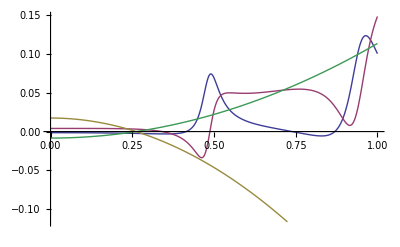

```mathematica
Plot[{Re[FO1[1,q]/F0[1,q]],Im[FO1[1,q]/F0[1,q]],Re[-I*ηO[1]*Z[1]^2*(1-q^2*(B+β[1]))/(k[1]*Sqrt[8*Pi*(B+β[1])])],Im[-I*ηO[1]*Z[1]^2*(1-q^2*(B+β[1]))/(k[1]*Sqrt[8*Pi*(B+β[1])])]},{q,0,1}]
```

```mathematica
FD1[1,0]/F0[1,0]
-I*ηD[1]*Z[1]^2/(k[1]*Sqrt[8*Pi*(B+β[1])])
```

0.0174106-0.00832509 ⅈ

```mathematica
F0[1,0]+FO1[1,0]+FD1[1,0]
```

-1.68566+6.89155 ⅈ

```mathematica
FO1[1,0]
```

-0.0248155-0.0154443 ⅈ

```mathematica
mult[x_]:={x[[1]]/1000.,x[[2]]}
σHe4NLP=ListLogLinearPlot[mult/@σHe4data];
```

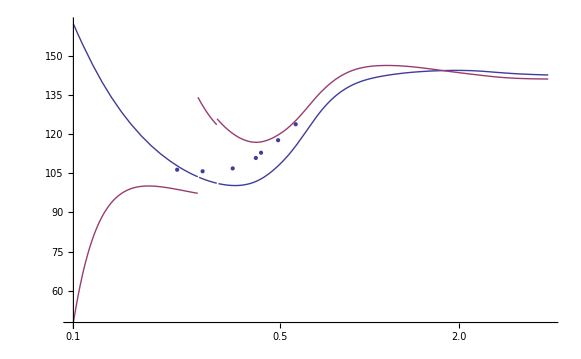

```mathematica
Show[LogLinearPlot[{(4*Pi)/(k[En]/ℏc)*Im[F0[En,0]]*10,(4*Pi)/(k[En]/ℏc)*Im[F0[En,0]+FO1[En,0]+FD1[En,0]]*10},{En,.1,4.01}],σHe4NLP]
```

This graph below should be a reproduction of Fig 3 from the Wallace. The uncorrected curve is pretty good, but the corrections don't seem to be correct.

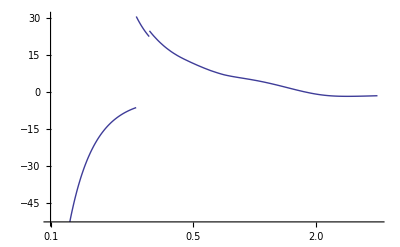

```mathematica
LogLinearPlot[(4*Pi)/(k[En]/ℏc)*Im[FO1[En,0]+FD1[En,0]]*10,{En,.1,4.01}]
```

```mathematica
(4*Pi)/(k[1]/ℏc)*Im[FO1[1,0]+FD1[1,0]]*10
```

4.74416

```mathematica
Im[(FD1[1,0]+FO1[1,0])]*4*Pi/(k[1]/ℏc)*10
```

4.74416

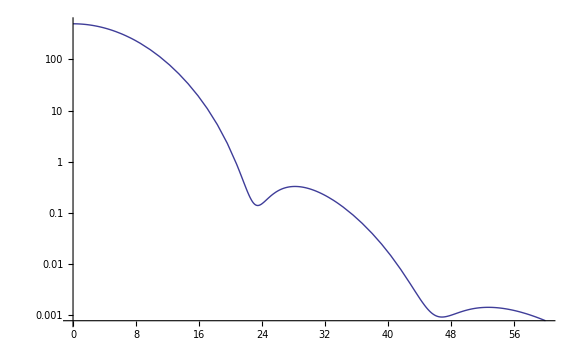

```mathematica
LogPlot[Abs[F0[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*10,{θ,0,60}]
```

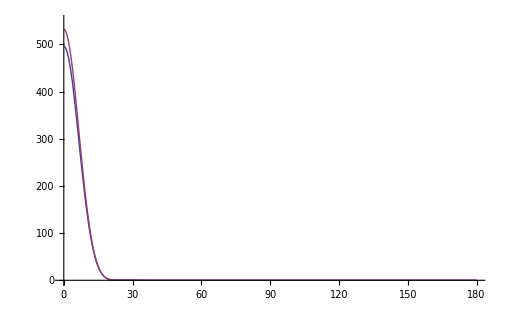

```mathematica
Plot[{Abs[F0[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*10,Abs[F0[1.05,2*k[1.05]*Sin[θ*Pi/360]]+FO1[1.05,2*k[1.05]*Sin[θ*Pi/360]]+FD1[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*10},{θ,0,180},PlotRange->{0,550}]
```

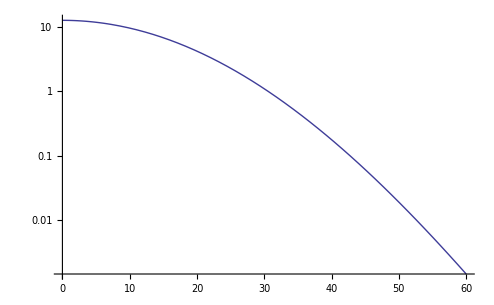

```mathematica
LogPlot[Abs[FD1[1.05,2*k[1.05]*Sin[θ*Pi/360]]]^2*200,{θ,0,60}]
```

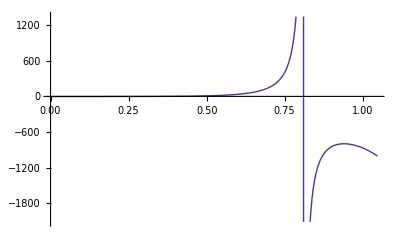

```mathematica
Plot[ηO[1.05]*(1-2*k[1.05]*Sin[t/2]^2*(B+β[1.05]))/(ηD[1.05]*(1-β[1.05]*2*k[1.05]*Sin[t/2]^2)*Exp[-B*2*k[1.05]*Sin[t/2]^2/2]/(A-1)),{t,0,Pi/3}]
```